```mathematica
f[x_,y_,{{x0_,y0_},r_}]:=(x-x0)^2+(y-y0)^2-r^2
```

```mathematica
v[{a1_,b1_},{a2_,b2_}]:={a2-a1,b2-b1}
```

```mathematica
fr[al_,{{x0_,y0_},r_}]:={r Cos[al]+x0,r Sin[al]+y0} 
m[fi_]:= {{Cos[fi],-Sin[fi]},{Sin[fi],Cos[fi]}}
```

```mathematica
curve[or1_,or2_,r1_,r2_,al_,bet_,gam_]:=Block[{},
o1o2=Norm[or2-or1];
rr1={or1,r1};rr2={or2,r2};
star=r1 Sin[Pi/2-al]-r2 Sin[Pi/2-bet];
fi = ArcCos[star/o1o2];
a=fr[al+fi,rr1];
b=fr[fi-bet,rr2];
p={a,b};
ab=Norm[v[a,b]];
rs=ab/2 1/Sin[(al+bet)/2];
R1=rs Sin[gam/2]/Sin[(al-bet+gam)/2];
R2=rs Sin[(al+bet-gam)/2]/Sin[bet-gam/2];

o1=#1+#3 v[#1,#2]/Norm[v[#1,#2]]&[a,or1, R1];
o2=#1+#3 v[#1,#2]/Norm[v[#1,#2]]&[b,or2, R2];
rR1={o1,R1};
rR2={o2,R2};
cplot = ContourPlot[Evaluate[(f[x,y,#]==0)&/@{rr1,rr2,rR1,rR2}],{x,-5,35},{y,-20,20},Epilog->Point[p]];

q = o1+v[o1,o2]/Norm[v[o1,o2]]If[R1>R2,1,-1]R1;

p={{-r1,0}-or1, a-o1,q-o2,b-or2};
po={or1,o1,o2,or2};
tet={VectorAngle[p[[1]],a],VectorAngle[-o1+a,-o1+q],VectorAngle[-o2+q,-o2+b],VectorAngle[-or2+b,-or2+{o1o2+r2,0}]};
dt=0.01  1/{r1,R1,R2,r2};
k= Abs[tet/dt];

point={};
Do[
s=p[[j]].m[dt[[j]]];
AppendTo[point,s+po[[j]]];
Do[s=s.m[dt[[j]]];
AppendTo[point,s+po[[j]]],{i,k[[j]]}],{j,4}];
point]
```

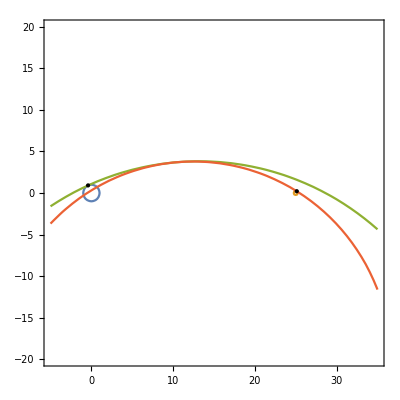

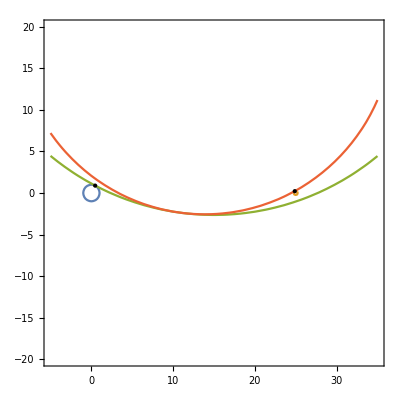

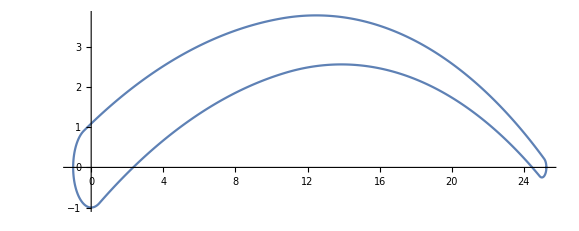

```mathematica
or1={0,0};or2={25,0};
r1=1;r2=0.25;
al=Pi/7. ;bet = Pi/6. ;gam=Pi/3. 0.4 ;
p1 = curve[or1,or2,r1,r2,al,bet,gam];
cplot
p2=curve[or1,or2,r1,r2,-al,-bet,-gam];
cplot
p2[[;;,2]]=-p2[[;;,2]];
p2=p2[[-1;;1;;-1]];
plot=Flatten[{p1,p2},1];
l = ListPlot[plot,Joined->True,AspectRatio->{1,1}]
```

```mathematica
dt
```

{0.01,-0.000314954,-0.000432594,0.04}

```mathematica
Export["curve.png",l]
```

curve.png

```mathematica
2 bet
bet - al
```

1.0472

0.0747998

```mathematica
gam
```

0.418879

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/godfather/Documents/TaskDash/Air

```mathematica
Export["curve.txt",plot,"Table"]
```

curve.txt

# zbs

```mathematica
f[x_,y_,{{x0_,y0_},r_}]:=(x-x0)^2+(y-y0)^2-r^2
```

```mathematica
v[{a1_,b1_},{a2_,b2_}]:={a2-a1,b2-b1}
```

```mathematica
fr[al_,{{x0_,y0_},r_}]:={r Cos[al]+x0,r Sin[al]+y0}
```

```mathematica
or1={0,0};or2={25,0};
o1o2=Norm[or2-or1]
```

25

```mathematica
r1=5;r2=2;
rr1={or1,r1};rr2={or2,r2};
al=-Pi/6. 1.55;bet = -Pi/3. 1;gam=-Pi/3. .5;
```

```mathematica
2 bet
bet - al
```

-2.0944

-0.235619

```mathematica
gam
```

-0.523599

```mathematica
star=r1 Sin[Pi/2-al]-r2 Sin[Pi/2-bet];
```

```mathematica
fi = ArcCos[star/o1o2];
a=fr[al+fi,rr1]
b=fr[fi-bet,rr2]
```

{3.94569,3.07108}

{23.3739,1.16439}

```mathematica
p={a,b};
```

```mathematica
ab=Norm[v[a,b]]
```

19.5215

```mathematica
rs=ab/2 1/Sin[(al+bet)/2]
```

-12.1819

```mathematica
R1=rs Sin[gam/2]/Sin[(al-bet+gam)/2]
R2=rs Sin[(al+bet-gam)/2]/Sin[bet-gam/2]
```

-21.9726

-10.6656

```mathematica
o1=#1+#3 v[#1,#2]/Norm[v[#1,#2]]&[a,or1, R1]
o2=#1+#3 v[#1,#2]/Norm[v[#1,#2]]&[b,or2, R2]
```

{21.2851,16.567}

{14.7022,7.37385}

```mathematica
rR1={o1,R1}
rR2={o2,R2}
```

{{21.2851,16.567},-21.9726}

{{14.7022,7.37385},-10.6656}

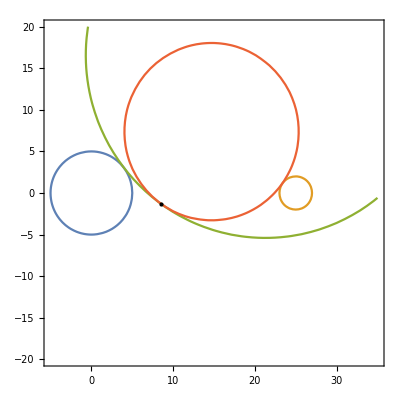

```mathematica
ContourPlot[Evaluate[(f[x,y,#]==0)&/@{rr1,rr2,rR1,rR2}],{x,-5,35},{y,-20,20},Epilog->Point[q]]
```

```mathematica
q = o1+v[o1,o2]/Norm[v[o1,o2]]If[R1>R2,1,-1]R1
```

{8.49277,-1.29781}

```mathematica
m[fi_]:= {{Cos[fi],-Sin[fi]},{Sin[fi],Cos[fi]}}
```

```mathematica
{1,0}.m[-Pi/2]
```

{0,1}

```mathematica
p={{-r1,0},a-o1,q-o2,b-or2};
```

```mathematica
po={or1,o1,o2,or2};
```

```mathematica
tet={VectorAngle[p[[1]],a],VectorAngle[-o1+a,-o1+q],VectorAngle[-o2+q,-o2+b],VectorAngle[-or2+b,-or2+{o1o2+r2,0}]}
```

{2.4802,0.287979,1.5708,2.52017}

```mathematica
dt=0.01  1/{r1,R1,R2,r2}
```

{0.002,-0.000455113,-0.000937593,0.005}

```mathematica
k= Abs[tet/dt]
```

{1240.1,632.764,1675.35,504.033}

```mathematica
point={};
Do[
s=p[[j]].m[dt[[j]]];
AppendTo[point,s+po[[j]]];
Do[s=s.m[dt[[j]]];
AppendTo[point,s+po[[j]]],{i,k[[j]]}],{j,4}]
```

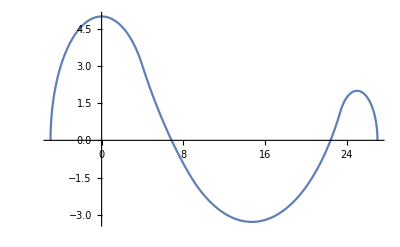

```mathematica
ListPlot[point,Joined->True]
```

```mathematica
point [[;;,2]]=-point[[;;,2]];
```

```mathematica
or1={0,0};or2={25,0};
o1o2=Norm[or2-or1]
```

25

```mathematica
r1=5;r2=2;
rr1={or1,r1};rr2={or2,r2};
al=Pi/6. 1.55;bet = Pi/3. 1;gam=Pi/3. .5;
```

```mathematica
2 bet
bet - al
```

2.0944

0.235619

```mathematica
gam
```

0.523599

```mathematica
star=r1 Sin[Pi/2-al]-r2 Sin[Pi/2-bet];
```

```mathematica
fi = ArcCos[star/o1o2];
a=fr[al+fi,rr1]
b=fr[fi-bet,rr2]
```

{-3.27337,3.77956}

{26.8214,0.826048}

```mathematica
p={a,b};
```

```mathematica
ab=Norm[v[a,b]]
```

30.2394

```mathematica
rs=ab/2 1/Sin[(al+bet)/2]
```

18.87

```mathematica
R1=rs Sin[gam/2]/Sin[(al-bet+gam)/2]
R2=rs Sin[(al+bet-gam)/2]/Sin[bet-gam/2]
```

34.0361

16.5213

```mathematica
o1=#1+#3 v[#1,#2]/Norm[v[#1,#2]]&[a,or1, R1]
o2=#1+#3 v[#1,#2]/Norm[v[#1,#2]]&[b,or2, R2]
```

{19.0092,-21.9487}

{11.7751,-5.99765}

```mathematica
rR1={o1,R1}
rR2={o2,R2}
```

{{19.0092,-21.9487},34.0361}

{{11.7751,-5.99765},16.5213}

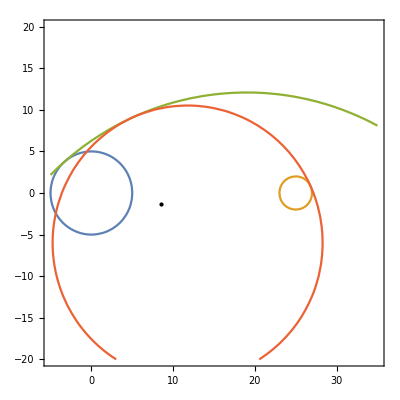

```mathematica
ContourPlot[Evaluate[(f[x,y,#]==0)&/@{rr1,rr2,rR1,rR2}],{x,-5,35},{y,-20,20},Epilog->Point[q]]
```

```mathematica
q = o1+v[o1,o2]/Norm[v[o1,o2]]If[R1>R2,1,-1]R1
```

{4.95145,9.04864}

```mathematica
m[fi_]:= {{Cos[fi],-Sin[fi]},{Sin[fi],Cos[fi]}}
```

```mathematica
{1,0}.m[-Pi/2]
```

{0,1}

```mathematica
p={{-r1,0},a-o1,q-o2,b-or2};
```

```mathematica
po={or1,o1,o2,or2};
```

```mathematica
tet={VectorAngle[p[[1]],a],VectorAngle[-o1+a,-o1+q],VectorAngle[-o2+q,-o2+b],VectorAngle[-or2+b,-or2+{o1o2+r2,0}]}
```

{0.857045,0.287979,1.5708,0.425772}

```mathematica
dt=0.01  1/{r1,R1,R2,r2}
```

{0.002,0.000293806,0.000605279,0.005}

```mathematica
k= Abs[tet/dt]
```

{428.523,980.169,2595.16,85.1544}

```mathematica
Do[
s=p[[j]].m[dt[[j]]];
AppendTo[point,s+po[[j]]];
Do[s=s.m[dt[[j]]];
AppendTo[point,s+po[[j]]],{i,k[[j]]}],{j,4}]
```

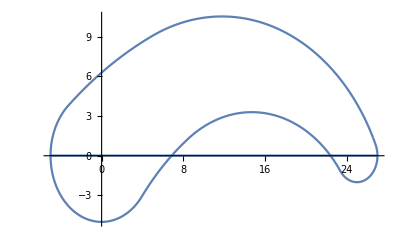

```mathematica
ListPlot[point,Joined->True]
```